```mathematica
B[tp]= {{Sqrt[d2], 0}, {0, K'[tp]*Sqrt[xi2]}}
s0=Array[Σ0,{2,2}]
```

{{√d2,0},{0,√xi2 K'[tp]}}

{{Σ0[1,1],Σ0[1,2]},{Σ0[2,1],Σ0[2,2]}}

```mathematica
A0[T] = {{0,T *λ},{-K0[T],T* λ+K0[T]}}
Atilde[tp]={{0, tp*λ},{-K[tp],K[tp]+tp*λ}}
```

{{0,T λ},{-K0[T],T λ+K0[T]}}

{{0,tp λ},{-K[tp],tp λ+K[tp]}}

```mathematica
FullSimplify[MatrixExp[-A0[T]]]
```

{{(ⅇ^(-K0[T]) T λ-ⅇ^(-T λ) K0[T])/(T λ-K0[T]),((ⅇ^(-T λ)-ⅇ^(-K0[T])) T λ)/(T λ-K0[T])},{-((ⅇ^(-T λ)-ⅇ^(-K0[T])) K0[T])/(T λ-K0[T]),(ⅇ^(-T λ) T λ-ⅇ^(-K0[T]) K0[T])/(T λ-K0[T])}}

```mathematica
Σ[T]=FullSimplify[MatrixExp[-A0[T]].s0.MatrixExp[-Transpose[A0[T]]]]+FullSimplify[Integrate[MatrixExp[-A0[T]+Atilde[tp]].B[tp].Transpose[B[tp]].MatrixExp[-Transpose[A0[T]]+Transpose[Atilde[tp]]], {tp, 0, T}]]
```

{{∫_0^T (d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K0[T]) T λ (K0[T] (-2 Σ0[1,1]+Σ0[1,2]+Σ0[2,1])+T λ (Σ0[1,2]+Σ0[2,1]-2 Σ0[2,2]))+ⅇ^(2 T λ) T^2 λ^2 (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])+ⅇ^(2 K0[T]) (K0[T]^2 Σ0[1,1]-T λ K0[T] (Σ0[1,2]+Σ0[2,1])+T^2 λ^2 Σ0[2,2])),∫_0^T (ⅇ^(-2 (T λ+K0[T])) (-ⅇ^(T λ+K[tp])+ⅇ^(tp λ+K0[T])) (ⅇ^(T λ+K[tp]) (T-tp) λ (K[tp]-K0[T]) (d2+xi2 K'[tp]^2)+ⅇ^(tp λ+K0[T]) (d2 (K[tp]-K0[T])^2+(T-tp)^2 xi2 λ^2 K'[tp]^2)))/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(2 T λ) T λ K0[T] (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])+ⅇ^(2 K0[T]) (K0[T]^2 Σ0[1,1]-T λ K0[T] (Σ0[1,2]+Σ0[2,1])+T^2 λ^2 Σ0[2,2])+ⅇ^(T λ+K0[T]) (K0[T]^2 (-Σ0[1,1]+Σ0[1,2])+T^2 λ^2 (Σ0[1,2]-Σ0[2,2])-T λ K0[T] (Σ0[1,1]-2 Σ0[2,1]+Σ0[2,2])))},{∫_0^T (ⅇ^(-2 (T λ+K0[T])) (-ⅇ^(T λ+K[tp])+ⅇ^(tp λ+K0[T])) (ⅇ^(T λ+K[tp]) (T-tp) λ (K[tp]-K0[T]) (d2+xi2 K'[tp]^2)+ⅇ^(tp λ+K0[T]) (d2 (K[tp]-K0[T])^2+(T-tp)^2 xi2 λ^2 K'[tp]^2)))/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(2 T λ) T λ K0[T] (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])+ⅇ^(2 K0[T]) (K0[T]^2 Σ0[1,1]-T λ K0[T] (Σ0[1,2]+Σ0[2,1])+T^2 λ^2 Σ0[2,2])+ⅇ^(T λ+K0[T]) (K0[T]^2 (-Σ0[1,1]+Σ0[2,1])+T^2 λ^2 (Σ0[2,1]-Σ0[2,2])-T λ K0[T] (Σ0[1,1]-2 Σ0[1,2]+Σ0[2,2]))),∫_0^T (d2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (K[tp]-K0[T])^2+xi2 (ⅇ^((-T+tp) λ) (T-tp) λ+ⅇ^(K[tp]-K0[T]) (K[tp]-K0[T]))^2 K'[tp]^2)/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^K0[T] T λ K0[T] (-ⅇ^K0[T] (Σ0[1,2]+Σ0[2,1])+ⅇ^(T λ) (Σ0[1,2]+Σ0[2,1]-2 Σ0[2,2]))+ⅇ^(2 K0[T]) T^2 λ^2 Σ0[2,2]+K0[T]^2 (ⅇ^(2 K0[T]) Σ0[1,1]+ⅇ^(T λ+K0[T]) (-2 Σ0[1,1]+Σ0[1,2]+Σ0[2,1])+ⅇ^(2 T λ) (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])))}}

```mathematica
%[[1,1]]
```

∫_0^T (d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K0[T]) T λ (K0[T] (-2 Σ0[1,1]+Σ0[1,2]+Σ0[2,1])+T λ (Σ0[1,2]+Σ0[2,1]-2 Σ0[2,2]))+ⅇ^(2 T λ) T^2 λ^2 (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])+ⅇ^(2 K0[T]) (K0[T]^2 Σ0[1,1]-T λ K0[T] (Σ0[1,2]+Σ0[2,1])+T^2 λ^2 Σ0[2,2]))

```mathematica
Needs["VariationalMethods`"]
```

EulerEquations::shdw: Symbol EulerEquations appears in multiple contexts {VariationalMethods`,Global`}; definitions in context VariationalMethods` may shadow or be shadowed by other definitions.

```mathematica
EulerEquations[(d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)/((T-tp) λ+K[tp]-K0[T])^2, K[tp], tp]
```

1/((T-tp) λ+K[tp]-K0[T])^3(4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp) xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K'[tp]-4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 (λ-K'[tp]) K'[tp]-4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T])) (T-tp)^2 xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K'[tp] (-ⅇ^(tp λ+K0[T]) λ+ⅇ^(T λ+K[tp]) K'[tp])+((T-tp) λ+K[tp]-K0[T]) (2 d2 (ⅇ^((-T+tp) λ)+ⅇ^(K[tp]-K0[T]) (T-tp) λ) (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))+2 ⅇ^(-T λ+K[tp]-2 K0[T]) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T])) (T-tp)^2 xi2 λ^2 K'[tp]^2)-2 (d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)-2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K''[tp])==0

```mathematica
Collect[%, {K[tp], K'[tp], K''[tp]}]
```

1/((T-tp) λ+K[tp]-K0[T])^3(4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp) xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K'[tp]-4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 (λ-K'[tp]) K'[tp]-4 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T])) (T-tp)^2 xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K'[tp] (-ⅇ^(tp λ+K0[T]) λ+ⅇ^(T λ+K[tp]) K'[tp])+((T-tp) λ+K[tp]-K0[T]) (2 d2 (ⅇ^((-T+tp) λ)+ⅇ^(K[tp]-K0[T]) (T-tp) λ) (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))+2 ⅇ^(-T λ+K[tp]-2 K0[T]) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T])) (T-tp)^2 xi2 λ^2 K'[tp]^2)-2 (d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)-2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 ((T-tp) λ+K[tp]-K0[T]) K''[tp])==0

```mathematica
params = {λ->1, xi2->10, d2->1, K0[T]->5}
```

{λ→1,xi2→10,d2→1,K0[T]→5}

```mathematica
eq =%4/. params
```

1/(-5+T-tp+K[tp])^3(40 ⅇ^(-2 (5+T)) (-ⅇ^(5+tp)+ⅇ^(T+K[tp]))^2 (T-tp) (-5+T-tp+K[tp]) K'[tp]-40 ⅇ^(-2 (5+T)) (-ⅇ^(5+tp)+ⅇ^(T+K[tp]))^2 (T-tp)^2 (1-K'[tp]) K'[tp]-40 ⅇ^(-2 (5+T)) (-ⅇ^(5+tp)+ⅇ^(T+K[tp])) (T-tp)^2 (-5+T-tp+K[tp]) K'[tp] (-ⅇ^(5+tp)+ⅇ^(T+K[tp]) K'[tp])+(-5+T-tp+K[tp]) (2 (ⅇ^(-T+tp)+ⅇ^(-5+K[tp]) (T-tp)) (ⅇ^(-5+K[tp]) (T-tp)+ⅇ^(-T+tp) (-5+K[tp]))+20 ⅇ^(-10-T+K[tp]) (-ⅇ^(5+tp)+ⅇ^(T+K[tp])) (T-tp)^2 K'[tp]^2)-2 ((ⅇ^(-5+K[tp]) (T-tp)+ⅇ^(-T+tp) (-5+K[tp]))^2+10 ⅇ^(-2 (5+T)) (-ⅇ^(5+tp)+ⅇ^(T+K[tp]))^2 (T-tp)^2 K'[tp]^2)-20 ⅇ^(-2 (5+T)) (-ⅇ^(5+tp)+ⅇ^(T+K[tp]))^2 (T-tp)^2 (-5+T-tp+K[tp]) K''[tp])==0

```mathematica
eq = eq/.T->10
```

1/(5-tp+K[tp])^3((40 (-ⅇ^(5+tp)+ⅇ^(10+K[tp]))^2 (10-tp) (5-tp+K[tp]) K'[tp])/ⅇ^30-(40 (-ⅇ^(5+tp)+ⅇ^(10+K[tp]))^2 (10-tp)^2 (1-K'[tp]) K'[tp])/ⅇ^30-(40 (-ⅇ^(5+tp)+ⅇ^(10+K[tp])) (10-tp)^2 (5-tp+K[tp]) K'[tp] (-ⅇ^(5+tp)+ⅇ^(10+K[tp]) K'[tp]))/ⅇ^30+(5-tp+K[tp]) (2 (ⅇ^(-10+tp)+ⅇ^(-5+K[tp]) (10-tp)) (ⅇ^(-5+K[tp]) (10-tp)+ⅇ^(-10+tp) (-5+K[tp]))+20 ⅇ^(-20+K[tp]) (-ⅇ^(5+tp)+ⅇ^(10+K[tp])) (10-tp)^2 K'[tp]^2)-2 ((ⅇ^(-5+K[tp]) (10-tp)+ⅇ^(-10+tp) (-5+K[tp]))^2+(10 (-ⅇ^(5+tp)+ⅇ^(10+K[tp]))^2 (10-tp)^2 K'[tp]^2)/ⅇ^30)-(20 (-ⅇ^(5+tp)+ⅇ^(10+K[tp]))^2 (10-tp)^2 (5-tp+K[tp]) K''[tp])/ⅇ^30)==0

```mathematica
Ksol[tp]=K[tp]/.First[NDSolve[{eq, K[0]==0, K'[0]==0.1}, K[tp], {tp, 0, 9}]]
```

InterpolatingFunction[…][tp]

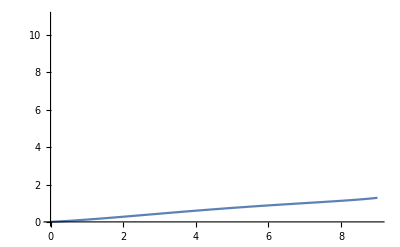

```mathematica
Plot[Ksol[tp], {tp, 0,9}, PlotRange->{0,11}]
```

```mathematica
ksol[tp]=D[Ksol[tp], tp]
```

InterpolatingFunction[…][tp]

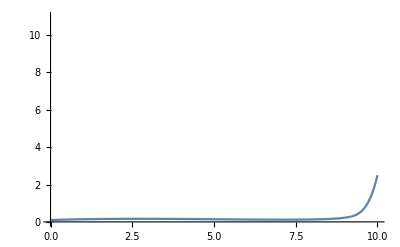

```mathematica
Plot[%142, {tp, 0,10}, PlotRange->{0,11}]
```

```mathematica
sigmaSol[T] = ∫_0^T (d2 (ⅇ^(K[tp]-K0[T]) (T-tp) λ+ⅇ^((-T+tp) λ) (K[tp]-K0[T]))^2+ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K[tp])-ⅇ^(tp λ+K0[T]))^2 (T-tp)^2 xi2 λ^2 K'[tp]^2)/((T-tp) λ+K[tp]-K0[T])^2 ⅆtp+1/(-T λ+K0[T])^2 ⅇ^(-2 (T λ+K0[T])) (ⅇ^(T λ+K0[T]) T λ (K0[T] (-2 Σ0[1,1]+Σ0[1,2]+Σ0[2,1])+T λ (Σ0[1,2]+Σ0[2,1]-2 Σ0[2,2]))+ⅇ^(2 T λ) T^2 λ^2 (Σ0[1,1]-Σ0[1,2]-Σ0[2,1]+Σ0[2,2])+ⅇ^(2 K0[T]) (K0[T]^2 Σ0[1,1]-T λ K0[T] (Σ0[1,2]+Σ0[2,1])+T^2 λ^2 Σ0[2,2]))/.{params, K[tp]->Ksol[tp], }
```